```mathematica
1 = 1;
mu2 = 1;
L1 = -50;
L2 = 50;
T = 1000;
x01 = 10;
sigma1 = 1;
x02 = -10;
sigma2 = 1;

f1 = 100;
f2 = 100;
f3 =   0 010.;

alpha1 = 1;
alpha2 =1;


gaussian[mu_, sigma_,x_] = 1 / (sigma Sqrt[2 π]) Exp[-(x - mu)^2  /(2 sigma^2)];
gaussianPrime[mu_, sigma_, x_] =(ⅇ^(-(-mu+x)^2/(2 sigma^2)) (-mu+x))/(√(2 π) sigma^3);

nestx0 = x01;
foodx0 = x02;
nestSigma = 1;
foodSigma = 1;
foodRate =1;
nestRate = 1;


food = foodRate * gaussian[foodx0, foodSigma, x];
nest = nestRate * gaussian[nestx0, nestSigma, x];


eq1 = D[c1[x,t],t] == mu1 * D[   D[c1[x,t],x] 
- f1 c1[x,t] D[c2[x,t] -alpha1 c1[x,t],x] - f3 (c1[x,t]) D[c1[x,t] + c2[x,t],x]  , x]+ c2[x,t]nest -c1[x,t]food;
ic1 = c1[x,0] ==gaussian[x01,sigma1,x];
bc1L = c1[L1,t] == gaussian[x01, sigma1, L1];
bc1R = c1[L2,t] == gaussian[x01, sigma1, L2];
bcSlope1L = Derivative[1,0][c1][L1,t] == 0;
bcSlope1R = Derivative[1,0][c1][L2,t] == 0;


eq2 = D[c2[x,t],t] == mu2 * D [D[c2[x,t],x]
 - f2 c2[x,t] D[c1[x,t] - alpha2 c2[x,t],x]  - f3 (c2[x,t]) D[c1[x,t] + c2[x,t],x] , x] + c1[x,t]food - c2[x,t]nest;
ic2 = c2[x,0] == gaussian[x02,sigma2,x];
bc2L = c2[L1,t] == gaussian[x02, sigma2, L1];
bc2R = c2[L2,t] == gaussian[x02, sigma2, L2];
bcSlope2L = Derivative[1,0][c2][L1,t] == 0;
bcSlope2R = Derivative[1,0][c2][L2,t] ==0;

sol = NDSolve[{eq1, ic1, bcSlope1L, bcSlope1R, eq2, ic2, bcSlope2L,  bcSlope2R},{c1, c2}, {x,L1, L2}, {t, 0, T}];


Manipulate[Plot[{Evaluate[c1[x,t]/. sol], Evaluate[c2[x,t]/. sol], Evaluate[(c1[x,t] +c2[x,t])/. sol], 0}, {x, L1, L2}, PlotRange->All], {t, 0, T}]
```

Set::setraw: Cannot assign to raw object 1.

ReplaceAll::reps: {sol} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Plot::plln: Limiting value L1 in {x, L1, L2} is not a machine-sized real number.

ReplaceAll::reps: {sol} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Plot::plln: Limiting value L1 in {x, L1, L2} is not a machine-sized real number.

ReplaceAll::reps: {sol} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Plot::plln: Limiting value L1 in {x, L1, L2} is not a machine-sized real number.

ReplaceAll::reps: {sol} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Plot::plln: Limiting value L1 in {x, L1, L2} is not a machine-sized real number.

ReplaceAll::reps: {sol} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Plot::plln: Limiting value L1 in {x, L1, L2} is not a machine-sized real number.

ReplaceAll::reps: {sol} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Plot::plln: Limiting value L1 in {x, L1, L2} is not a machine-sized real number.

NDSolve::deqn: Equation or list of equations expected instead of ic2 in the first argument SuperscriptBox[SuperscriptBox[SuperscriptBox[C2[x, 0, 0, 0] == 1SuperscriptBox[SuperscriptBox[SuperscriptBox[ic2.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

NDSolve::deqn: Equation or list of equations expected instead of ic2 in the first argument SuperscriptBox[SuperscriptBox[SuperscriptBox[C2[x, 0, 0, 0] == 1SuperscriptBox[SuperscriptBox[SuperscriptBox[ic2.

General::stop: Further output of NDSolve :: deqn will be suppressed during this calculation.

Plot::plln: Limiting value L1 in {x, L1, L2} is not a machine-sized real number.

NDSolve::ndode: Input is not an ordinary differential equation.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

NDSolve::ndode: Input is not an ordinary differential equation.

General::stop: Further output of NDSolve :: ndode will be suppressed during this calculation.

Plot::plln: Limiting value L1 in {x, L1, L2} is not a machine-sized real number.

NDSolve::ndode: Input is not an ordinary differential equation.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

NDSolve::ndode: Input is not an ordinary differential equation.

General::stop: Further output of NDSolve :: ndode will be suppressed during this calculation.

Plot::plln: Limiting value L1 in {x, L1, L2} is not a machine-sized real number.

NDSolve::ndode: Input is not an ordinary differential equation.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

NDSolve::ndode: Input is not an ordinary differential equation.

General::stop: Further output of NDSolve :: ndode will be suppressed during this calculation.

Plot::plln: Limiting value L1 in {x, L1, L2} is not a machine-sized real number.

NDSolve::ndode: Input is not an ordinary differential equation.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

NDSolve::ndode: Input is not an ordinary differential equation.

General::stop: Further output of NDSolve :: ndode will be suppressed during this calculation.

Plot::plln: Limiting value L1 in {x, L1, L2} is not a machine-sized real number.

ReplaceAll::reps: {sol} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Plot::plln: Limiting value L1 in {x, L1, L2} is not a machine-sized real number.

NDSolve::ndode: Input is not an ordinary differential equation.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

NDSolve::ndode: Input is not an ordinary differential equation.

General::stop: Further output of NDSolve :: ndode will be suppressed during this calculation.

Plot::plln: Limiting value L1 in {x, L1, L2} is not a machine-sized real number.

NDSolve::ndode: Input is not an ordinary differential equation.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

NDSolve::ndode: Input is not an ordinary differential equation.

General::stop: Further output of NDSolve :: ndode will be suppressed during this calculation.

Plot::plln: Limiting value L1 in {x, L1, L2} is not a machine-sized real number.

NDSolve::ndode: Input is not an ordinary differential equation.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

NDSolve::ndode: Input is not an ordinary differential equation.

General::stop: Further output of NDSolve :: ndode will be suppressed during this calculation.

Plot::plln: Limiting value L1 in {x, L1, L2} is not a machine-sized real number.

NDSolve::ndode: Input is not an ordinary differential equation.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

NDSolve::ndode: Input is not an ordinary differential equation.

General::stop: Further output of NDSolve :: ndode will be suppressed during this calculation.

Plot::plln: Limiting value L1 in {x, L1, L2} is not a machine-sized real number.

NDSolve::derlen: The length of the derivative operator Derivative[1, 0, 0] in SuperscriptBox[ is not the same as the number of arguments.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

NDSolve::derlen: The length of the derivative operator Derivative[1, 0, 0] in SuperscriptBox[ is not the same as the number of arguments.

General::stop: Further output of NDSolve :: derlen will be suppressed during this calculation.

Plot::plln: Limiting value L1 in {x, L1, L2} is not a machine-sized real number.

NDSolve::derlen: The length of the derivative operator Derivative[1, 0, 0] in SuperscriptBox[ is not the same as the number of arguments.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

NDSolve::derlen: The length of the derivative operator Derivative[1, 0, 0] in SuperscriptBox[ is not the same as the number of arguments.

General::stop: Further output of NDSolve :: derlen will be suppressed during this calculation.

Plot::plln: Limiting value L1 in {x, L1, L2} is not a machine-sized real number.

NDSolve::dvlen: The function SuperscriptBox[ does not have the same number of arguments as independent variables (2).

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

NDSolve::dvlen: The function SuperscriptBox[ does not have the same number of arguments as independent variables (2).

General::stop: Further output of NDSolve :: dvlen will be suppressed during this calculation.

Plot::plln: Limiting value L1 in {x, L1, L2} is not a machine-sized real number.

NDSolve::bcedge: Boundary condition SuperscriptBox[ is not specified on a single edge of the boundary of the computational domain.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

NDSolve::bcedge: Boundary condition SuperscriptBox[ is not specified on a single edge of the boundary of the computational domain.

General::stop: Further output of NDSolve :: bcedge will be suppressed during this calculation.

Plot::plln: Limiting value L1 in {x, L1, L2} is not a machine-sized real number.

NDSolve::bcedge: Boundary condition SuperscriptBox[ is not specified on a single edge of the boundary of the computational domain.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

NDSolve::bcedge: Boundary condition SuperscriptBox[ is not specified on a single edge of the boundary of the computational domain.

General::stop: Further output of NDSolve :: bcedge will be suppressed during this calculation.

Plot::plln: Limiting value L1 in {x, L1, L2} is not a machine-sized real number.

NDSolve::bcedge: Boundary condition SuperscriptBox[ is not specified on a single edge of the boundary of the computational domain.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

NDSolve::bcedge: Boundary condition SuperscriptBox[ is not specified on a single edge of the boundary of the computational domain.

General::stop: Further output of NDSolve :: bcedge will be suppressed during this calculation.

Plot::plln: Limiting value L1 in {x, L1, L2} is not a machine-sized real number.

NDSolve::bcedge: Boundary condition SuperscriptBox[ is not specified on a single edge of the boundary of the computational domain.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

NDSolve::bcedge: Boundary condition SuperscriptBox[ is not specified on a single edge of the boundary of the computational domain.

General::stop: Further output of NDSolve :: bcedge will be suppressed during this calculation.

Plot::plln: Limiting value L1 in {x, L1, L2} is not a machine-sized real number.

NDSolve::bcedge: Boundary condition SuperscriptBox[ is not specified on a single edge of the boundary of the computational domain.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

NDSolve::bcedge: Boundary condition SuperscriptBox[ is not specified on a single edge of the boundary of the computational domain.

General::stop: Further output of NDSolve :: bcedge will be suppressed during this calculation.

Plot::plln: Limiting value L1 in {x, L1, L2} is not a machine-sized real number.

ReplaceAll::reps: DSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

DSolve::dsvar: {x, -10, 10} cannot be used as a variable.

General::stop: Further output of DSolve :: dsvar will be suppressed during this calculation.

Plot::plln: Limiting value L1 in {x, L1, L2} is not a machine-sized real number.

ReplaceAll::reps: DSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Plot::plln: Limiting value L1 in {x, L1, L2} is not a machine-sized real number.

NDSolve::femcnsd: The PDE coefficient C[2 x, t] does not evaluate to a numeric scalar.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::femcnsd: The PDE coefficient C[2 x, t] does not evaluate to a numeric scalar.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::femcnsd: The PDE coefficient C[2 x, t] does not evaluate to a numeric scalar.

General::stop: Further output of NDSolve :: femcnsd will be suppressed during this calculation.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Plot::plln: Limiting value L1 in {x, L1, L2} is not a machine-sized real number.

NDSolve::femcnsd: The PDE coefficient C[2 x, t] does not evaluate to a numeric scalar.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::femcnsd: The PDE coefficient C[2 x, t] does not evaluate to a numeric scalar.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::femcnsd: The PDE coefficient C[2 x, t] does not evaluate to a numeric scalar.

General::stop: Further output of NDSolve :: femcnsd will be suppressed during this calculation.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Plot::plln: Limiting value L1 in {x, L1, L2} is not a machine-sized real number.

NDSolve::femcnsd: The PDE coefficient C[2 x, t] does not evaluate to a numeric scalar.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::femcnsd: The PDE coefficient C[2 x, t] does not evaluate to a numeric scalar.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::femcnsd: The PDE coefficient C[2 x, t] does not evaluate to a numeric scalar.

General::stop: Further output of NDSolve :: femcnsd will be suppressed during this calculation.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Plot::plln: Limiting value L1 in {x, L1, L2} is not a machine-sized real number.

NDSolve::femcnsd: The PDE coefficient C[x, t] does not evaluate to a numeric scalar.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::femcnsd: The PDE coefficient C[x, t] does not evaluate to a numeric scalar.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::femcnsd: The PDE coefficient C[x, t] does not evaluate to a numeric scalar.

General::stop: Further output of NDSolve :: femcnsd will be suppressed during this calculation.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Plot::plln: Limiting value L1 in {x, L1, L2} is not a machine-sized real number.

NDSolve::femcnsd: The PDE coefficient C[x, t] does not evaluate to a numeric scalar.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::femcnsd: The PDE coefficient C[x, t] does not evaluate to a numeric scalar.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::femcnsd: The PDE coefficient C[x, t] does not evaluate to a numeric scalar.

General::stop: Further output of NDSolve :: femcnsd will be suppressed during this calculation.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Plot::plln: Limiting value L1 in {x, L1, L2} is not a machine-sized real number.

NDSolve::femcnsd: The PDE coefficient C[x, t] does not evaluate to a numeric scalar.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::femcnsd: The PDE coefficient C[x, t] does not evaluate to a numeric scalar.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::femcnsd: The PDE coefficient C[x, t] does not evaluate to a numeric scalar.

General::stop: Further output of NDSolve :: femcnsd will be suppressed during this calculation.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Plot::plln: Limiting value L1 in {x, L1, L2} is not a machine-sized real number.

```mathematica
bcSlope2L = Derivative[1,0][c2][L1,t] == gaussianPrime[x02, sigma2, L1];
bcSlope2R = Derivative[1,0][c2][L2,t] == gaussianPrime[x02, sigma2, L2];
bcSlope1L = Derivative[1,0][c1][L1,t] == gaussianPrime[x01, sigma1, L1];
bcSlope1R = Derivative[1,0][c1][L2,t] == gaussianPrime[x01, sigma1, L2];
```

## In terms of sum and difference variables. c1 = sum, c2 = diff (food - no food)

```mathematica
mu1 = 1;
L1 = -50;
L2 = 50;
T = 1000;
x01 = 10;
sigma1 = 1;
x02 = -10;
sigma2 = 1;

f = 100;

gaussian[mu_, sigma_,x_] = 1 / (sigma Sqrt[2 π]) Exp[-(x - mu)^2  /(2 sigma^2)];

nestx0 = x01;
foodx0 = x02;
nestSigma = 1;
foodSigma = 1;
foodRate =1;
nestRate = 1;


oldfood = foodRate * gaussian[foodx0, foodSigma, x];
food = foodRate * Piecewise[{{(1 - Cos[24π( x-L1) /(2 L2)])^2,x<0}, {0, x≥0}}] ;
nest = nestRate * gaussian[nestx0, nestSigma, x];


eq1 = D[c1[x,t],t] ==  D[  mu1  D[c1[x,t],x] + f c2[x,t] D[c2[x,t],x],x] ;
ic1 = c1[x,0] ==gaussian[x01,sigma1,x] + gaussian[x02,sigma2,x] ;
bc1L = c1[L1,t] ==gaussian[x01,sigma1,L1] + gaussian[x02,sigma2,L1] ;
bc1R = c1[L2,t] == gaussian[x01,sigma1,L2] + gaussian[x02,sigma2,L2] ;
bcSlope1L = Derivative[1,0][c1][L1,t] == 0;
bcSlope1R = Derivative[1,0][c1][L2,t] == 0;


eq2 = D[c2[x,t],t] ==  D[  mu1  D[c2[x,t],x] + f c1[x,t] D[c2[x,t],x],x]+ c1[x,t](nest -food) - c2[x,t](food + nest);
ic2 = c2[x,0] ==gaussian[x01,sigma1,x]- gaussian[x02,sigma2,x] ;
bc2L = c2[L1,t] == gaussian[x01,sigma1,L1] - gaussian[x02,sigma2,L1] ;
bc2R = c2[L2,t] == gaussian[x01,sigma1,L2] - gaussian[x02,sigma2,L2] ;
bcSlope2L = Derivative[1,0][c2][L1,t] == 0;
bcSlope2R = Derivative[1,0][c2][L2,t] ==0;

sol = NDSolve[{eq1, ic1, bcSlope1L, bcSlope1R, eq2, ic2, bcSlope2L,  bcSlope2R},{c1, c2}, {x,L1, L2}, {t, 0, T}];


Manipulate[Plot[{Evaluate[c1[x,t]/. sol], Evaluate[c2[x,t]/. sol], 0}, {x, L1, L2}, PlotRange->All], {t, 0, T}]
```

## 2 dimensional. Better version in terms of density and order parameter further down.

```mathematica
mu1 = 1;
mu2 = 1;
L1 = -50;
L2 = 50;
T = 1;
x01 = 10;
y01 = 0;
sigma1 = 1;
x02 = -10;
y02 = -0;
sigma2 = 1;

f1 = 0;
f2 = 0;

alpha1 = 0;
alpha2 =0;


gaussian[mux_,muy_, sigma_,x_, y_] = 1 / (sigma Sqrt[2 π]) Exp[-((x - mux)^2  +(y-muy)^2)/(2 sigma^2)];


nestx0 = x01;
foodx0 = x02;
nesty0 = y01;
foody0 = y02;
nestSigma = 1;
foodSigma = 1;
foodRate =0;
nestRate = 0;


food = foodRate * gaussian[foodx0,foody0, foodSigma, x, y];
nest = nestRate * gaussian[nestx0,nesty0, nestSigma, x, y];


eq1 = D[c1[x,y,t],t] == mu1 * D[   D[c1[x,y,t],x] 
- f1 c1[x,y,t] D[c2[x,y,t] -alpha1 c1[x,y, t],x]  , x]+ mu1 * D[   D[c1[x,y,t],y] 
- f1 c1[x,y,t] D[c2[x,y,t] -alpha1 c1[x,y, t],y]  , y]+ c2[x,y,t]nest -c1[x,y,t]food;
ic1 = c1[x,y,0] == gaussian[x01,y01,sigma1,x,y];
bcSlope1xL = Derivative[1,0,0][c1][L1,y,t] == 0;
bcSlope1xR = Derivative[1,0,0][c1][L2,y,t] == 0;
bcSlope1yL = Derivative[0,1,0][c1][x,L1,t] == 0;
bcSlope1yR = Derivative[0,1,0][c1][x,L2,t] == 0;


eq2 = D[c2[x,y,t],t] == mu2 * D[   D[c2[x,y,t],x] 
- f2 c2[x,y,t] D[c1[x,y,t] -alpha1 c2[x,y, t],x]  , x]+ mu2 * D[   D[c2[x,y,t],y] 
- f2 c2[x,y,t] D[c1[x,y,t] -alpha1 c2[x,y, t],y]  , y]- c2[x,y,t]nest +c1[x,y,t]food;
ic2 = c2[x,y,0] == gaussian[x02,y02,sigma2,x,y];
bcSlope2xL = Derivative[1,0,0][c2][L1,y,t] == 0;
bcSlope2xR = Derivative[1,0,0][c2][L2,y,t] == 0;
bcSlope2yL = Derivative[0,1,0][c2][x,L1,t] == 0;
bcSlope2yR = Derivative[0,1,0][c2][x,L2,t] == 0;



sol = NDSolve[{eq1, ic1, bcSlope1xL, bcSlope1xR,bcSlope1yL, bcSlope1yR, eq2, ic2, bcSlope2xL,  bcSlope2xR, bcSlope2yL, bcSlope2yR},{c1, c2}, {x,L1, L2},{y,L1,L2}, {t, 0, T}];
Manipulate[Plot3D[Evaluate[c1[x,y,t]/. sol], {x, L1, L2},{y,L1,L2}, Mesh->50,PlotRange->All], {t, 0, T}]
Manipulate[Plot3D[Evaluate[c2[x,y,t]/. sol], {x, L1, L2},{y,L1,L2}, Mesh->50], {t, 0, T}]
```

NDSolve::mxsst: Using maximum number of grid points 100 allowed by the MaxPoints or MinStepSize options for independent variable x.

NDSolve::mxsst: Using maximum number of grid points 100 allowed by the MaxPoints or MinStepSize options for independent variable y.

NDSolve::mxsst: Using maximum number of grid points 100 allowed by the MaxPoints or MinStepSize options for independent variable x.

General::stop: Further output of NDSolve :: mxsst will be suppressed during this calculation.

## 2 dim in terms of sum and diff

```mathematica
mu1 = .2;
L1 = -90;
L2 = 90;
T = 800;
x01 = 25;
y01 = 10;
sigma1 = 10;
x02 = -25;
y02 = -10;
sigma2 = 10;

f = 2;

gaussian[mux_,muy_, sigma_,x_, y_] = 1 / (sigma Sqrt[2 π])^2 Exp[-((x - mux)^2  +(y-muy)^2)/(2 sigma^2)];


nestx0 = x02;
nesty0 = y02;
foodx0 = x01;
foody0 = y01;
nestSigma = 10;
foodSigma = 10;
foodRate =10;
nestRate = 10;




food = foodRate * gaussian[foodx0,foody0, foodSigma, x,y];
nest = nestRate * gaussian[nestx0, nesty0, nestSigma, x,y];


eq1 = D[c1[x,y,t],t] ==    mu1( D[c1[x,y,t],{x,2}]+ D[c1[x,y,t],{y,2}]) + f D[c2[x,y,t] D[c2[x,y,t],x],x]+ f D[c2[x,y,t] D[c2[x,y,t],y],y] ;
ic1 = c1[x,y,0] ==gaussian[x01,y01,sigma1,x,y] + 0*gaussian[x02,y02,sigma2,x,y] ;
bcSlope1xL = Derivative[1,0,0][c1][L1,y,t] == 0;
bcSlope1xR = Derivative[1,0,0][c1][L2,y,t] == 0;
bcSlope1yL = Derivative[0,1,0][c1][x,L1,t] == 0;
bcSlope1yR = Derivative[0,1,0][c1][x,L2,t] == 0;
bc = Derivative[1,1,0][c1][L1,y,t] == 0;
bc2 = Derivative[1,1,0][c1][L2,y,t] == 0;
bc3 = Derivative[1,1,0][c1][x,L1,t] == 0;
bc4 = Derivative[1,1,0][c1][x,L2,t] == 0;



eq2 = D[c2[x,y,t],t] ==  mu1 ( D[c2[x,y,t],{x,2}]+D[c2[x,y,t],{y,2}]) + D[f c1[x,y,t] D[c2[x,y,t],x],x]+ D[f c1[x,y,t] D[c2[x,y,t],y],y]+ c1[x,y,t](nest -food) - c2[x,y,t](food + nest);
ic2 = c2[x,y,0] ==gaussian[x01,y01,sigma1,x,y]- gaussian[x02,y02,sigma2,x,y] ;
bcSlope2xL = Derivative[1,0,0][c2][L1,y,t] == 0;
bcSlope2xR = Derivative[1,0,0][c2][L2,y,t] == 0;
bcSlope2yL = Derivative[0,1,0][c2][x,L1,t] == 0;
bcSlope2yR = Derivative[0,1,0][c2][x,L2,t] == 0;

sol = NDSolve[{eq1, ic1, bcSlope1xL, bcSlope1xR,bcSlope1yL, bcSlope1yR,eq2, ic2, bcSlope2xL,  bcSlope2xR, bcSlope2yL, bcSlope2yR},{c1, c2}, {x,L1, L2},{y,L1,L2}, {t, 0, T}];
Manipulate[ContourPlot[Evaluate[c1[x,y,t]/. sol], {x, L1, L2},{y,L1,L2},PlotRange->All, Mesh->50], {t, 0, T}]
Manipulate[ContourPlot[Evaluate[c2[x,y,t]/. sol], {x, L1, L2},{y,L1,L2},PlotRange->All,Mesh->50], {t, 0, T}]
```

```mathematica
Manipulate[Plot3D[Evaluate[c1[x,y,t]/. sol], {x, L1, L2},{y,L1,L2},PlotRange->All, Mesh->50], {t, 0, T}]
Manipulate[Plot3D[Evaluate[c2[x,y,t]/. sol], {x, L1, L2},{y,L1,L2},PlotRange->All,Mesh->50], {t, 0, T}]
```

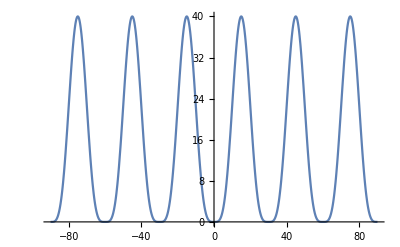

```mathematica
Plot[ foodRate * (1 - Cos[12 π( x-L1) /(2 L2)])^2,{x,L1,L2}]
```